# 1 - Tight Binding

## a) Desenho das bandas

```mathematica
latticeVec={{(√3)/2,-1/2},{(√3)/2,1/2}} ;  (*lattice*)
reciprocalVec= 2 π Transpose[Inverse[latticeVec]]    ;(*reciprocal lattice*)
recvolume=Det[reciprocalVec];
nsize=3 ; (*increase it as needed*)
indicesTri=Flatten[Outer[List,Table[i,{i,-nsize,nsize}],Table[i,{i,-nsize,nsize}]],1];
gspaceVec=indicesTri.reciprocalVec;
ng=Dimensions[gspaceVec][[1]];
```

```mathematica
f=Function[{x,y},
Module[{nc,j},nc=0;Do[If[{x,y}.gspaceVec⟦j⟧>1/2 gspaceVec⟦j⟧.gspaceVec⟦j⟧,nc=nc+1],{j,1,ng}];nc]];
```

```mathematica
h2[k_,t2_]:=({{-2t2(Cos[k.latticeVec[[1]]] + Cos[k.latticeVec[[2]] ] + Cos[k.(latticeVec[[1]]-latticeVec[[2]])]), -(1+Exp[-I k.latticeVec[[1]]]+Exp[-I k.latticeVec[[2]]])}, {-(1+Exp[I k.latticeVec[[1]]]+Exp[I k.latticeVec[[2]]]), -2t2(Cos[k.latticeVec[[1]]] + Cos[k.latticeVec[[2]] ] + Cos[k.(latticeVec[[1]]-latticeVec[[2]])])}})
```

```mathematica
S[k_,s_]:= ({{1, s(1+Exp[-I k.latticeVec[[1]]]+Exp[-I k.latticeVec[[2]]])}, {s(1+Exp[I k.latticeVec[[1]]]+Exp[I k.latticeVec[[2]]]), 1}});
```

### t2 = 0

```mathematica
s=0.1;
t2=0;
kGammaM[q_]:= q/2(reciprocalVec[[1]]+reciprocalVec[[2]]);
kGammaK[q_]:= q/3(2reciprocalVec[[1]]+reciprocalVec[[2]]);
```

#### Caminho Γ-M

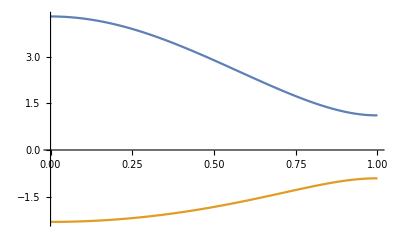

```mathematica
Plot[Evaluate[Sort[Eigenvalues[{h2[kGammaM[q],t2],S[kGammaM[q],s]}   ]]],{q,0,1}]
```

#### Caminho Γ - K

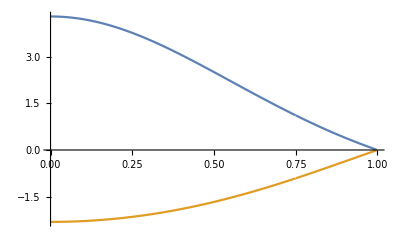

```mathematica
Plot[Evaluate[Sort[Eigenvalues[{h2[kGammaK[q],t0],S[kGammaK[q],s0]}   ]/.{s0->s,t0->t2}]],{q,0,1}]
```

### t2 != 0

#### Caminho Γ-M

```mathematica
s=0.1;
t2=0.03*4;
```

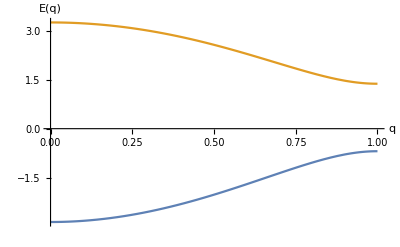

```mathematica
Plot[Evaluate[Sort[Eigenvalues[{h2[kGammaM[q],t02],S[kGammaM[q],s0]}]]/.{s0->s,t02->t2}],{q,0,1},AxesLabel->((Style[#,15])&/@{"q","E(q)"})]
```

#### Caminho Γ - K

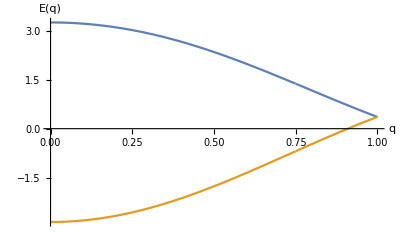

```mathematica
Plot[Evaluate[Sort[Eigenvalues[{h2[kGammaK[q],t02],S[kGammaK[q],s0]}]]/.{s0->s,t02->t2}],{q,0,1},AxesLabel->((Style[#,15])&/@{"q","E(q)"})]
```

#### Caminho Γ - K - M - Γ (comparação)

```mathematica
kGammaMKGamma[q_]:= Piecewise[{{kGammaK[q],q<=1},{(2-q)kGammaK[1] +(q-1)(kGammaM[1]),1<q<=2},{kGammaM[3-q],2<q<=3}}];
```

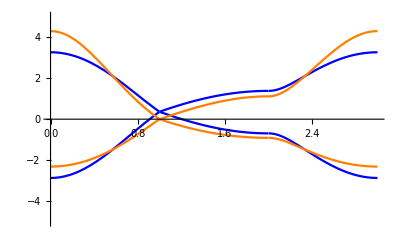

```mathematica
Show[Plot[Evaluate[Sort[Evaluate[Eigenvalues[{Evaluate@h2[kGammaMKGamma[q],t0],Evaluate@S[kGammaMKGamma[q],s0]} ]]/.{s0->s,t0->t2}]],{q,0,3},PlotStyle->Blue,PlotRange->{-5,5}],Plot[Evaluate[Sort[Evaluate[Eigenvalues[{Evaluate@h2[kGammaMKGamma[q],t0],Evaluate@S[kGammaMKGamma[q],s0]} ]]/.{s0->s,t0->0}]],{q,0,3},PlotStyle->Orange]]
```

## b) Desenho 3D

```mathematica
s=0.1;
t2=0.03*4;
Plot3D[Evaluate[Sort[Eigenvalues[{h2[{kx,ky},t0],S[{kx,ky},s0]}]]/.{s0->s,t0->t2}],{kx,-6,6},{ky,-6,6},
RegionFunction->Function[{kx,ky},f[kx,ky]<0.5],BoxRatios->{1,1,0.8},ImageSize->Medium,MeshFunctions->{#3&},Mesh->11]
```

-Graphics3D-

# 2 - Plane Waves

## a) Energias dos estados estacionários

```mathematica
e0 = ((6.58*^-16)^2)/(511*^3/(2.997*^8)^2*(1.455*^-10)^2)
d =31.8/e0
V1[z_]:=-d Exp[-z^2]+d
ℒ=-u''[z]/2+V1[z]*u[z];
```

3.59483

8.84604

```mathematica
d*e0
```

31.8

```mathematica
e0SI = ((1.055*^-34)^2)/((9.109*^-31)*(1.455*^-10)^2)
```

5.77176×10^-19

```mathematica
dSI=(31.8*1.6*^-19)/e0SI
```

8.81534

Resolver equação impondo que função de onda se anule em z = 100 e z = -100

```mathematica
{energies,wavefunctions}=NDEigensystem[ℒ,u[z],{z,-100,100},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[«1»] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

3 Primeiros Valores próprios de energia :

```mathematica
energies-d
```

{-6.93171,-3.52937,-1.08015,0.000153115,0.00153598,0.00296326,0.0082975,0.0126117,0.0169566,0.0260879}

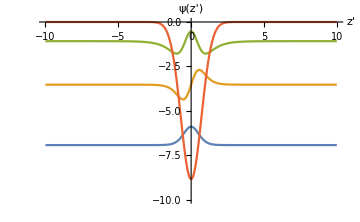

```mathematica
Show[Plot[{Evaluate[wavefunctions[[1;;3]]+energies[[1;;3]]-d],V1[z]-d},{z,-10,10},PlotRange->All],PlotRange->{{-10,10},{-10,0}},AxesOrigin->{0,0},ImageSize->Medium,AxesLabel->Evaluate[Style[#,15]&/@{"z'","ψ(z')"}]]
```

```mathematica
E1=(energies-d)[[1]]
```

-6.93171

```mathematica
E2=(energies-d)[[2]]
```

-3.52937

```mathematica
E3=(energies-d)[[3]]
```

-1.08015

```mathematica
ka= 1.455^2/2.46^2;
```

```mathematica
Kin[{kx_,ky_}]:=1/2*ka*(kx^2+ky^2);
```

## b) Bandas de energia

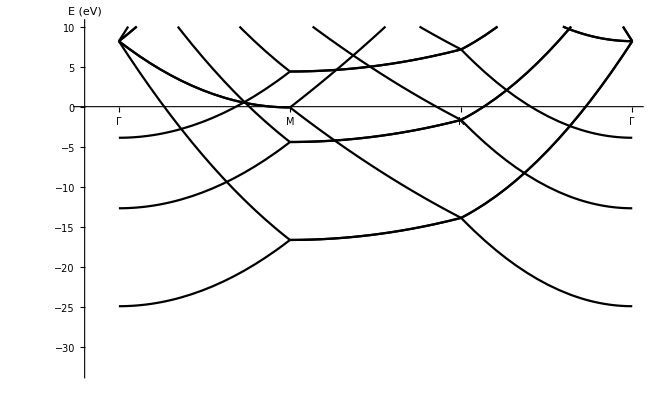

```mathematica
Plot[e0{E1+Kin[kGammaMKGamma[3-q]],E2+Kin[kGammaMKGamma[3-q]],E3+Kin[kGammaMKGamma[3-q]],E1+Kin[kGammaMKGamma[3-q]-reciprocalVec[[1]]],E2+Kin[kGammaMKGamma[3-q]-reciprocalVec[[1]]],
E3+Kin[kGammaMKGamma[3-q]-reciprocalVec[[1]]],
E1+Kin[kGammaMKGamma[3-q]+reciprocalVec[[1]]],E2+Kin[kGammaMKGamma[3-q]+reciprocalVec[[1]]],
E3+Kin[kGammaMKGamma[3-q]+reciprocalVec[[1]]],
E1+Kin[kGammaMKGamma[3-q]-reciprocalVec[[2]]],E2+Kin[kGammaMKGamma[3-q]-reciprocalVec[[2]]],
E3+Kin[kGammaMKGamma[3-q]-reciprocalVec[[2]]],
E1+Kin[kGammaMKGamma[3-q]+reciprocalVec[[2]]],E2+Kin[kGammaMKGamma[3-q]+reciprocalVec[[2]]],
E3+Kin[kGammaMKGamma[3-q]+reciprocalVec[[2]]],
E1+Kin[kGammaMKGamma[3-q]-reciprocalVec[[1]]+reciprocalVec[[2]]],E2+Kin[kGammaMKGamma[3-q]-reciprocalVec[[1]]+reciprocalVec[[2]]],
E3+Kin[kGammaMKGamma[3-q]-reciprocalVec[[1]]+reciprocalVec[[2]]],
E1+Kin[kGammaMKGamma[3-q]-reciprocalVec[[1]]-reciprocalVec[[2]]],E2+Kin[kGammaMKGamma[3-q]-reciprocalVec[[1]]-reciprocalVec[[2]]],
E3+Kin[kGammaMKGamma[3-q]-reciprocalVec[[1]]-reciprocalVec[[2]]],
E1+Kin[kGammaMKGamma[3-q]+reciprocalVec[[1]]+reciprocalVec[[2]]],E2+Kin[kGammaMKGamma[3-q]+reciprocalVec[[1]]+reciprocalVec[[2]]],
E3+Kin[kGammaMKGamma[3-q]+reciprocalVec[[1]]+reciprocalVec[[2]]],
E1+Kin[kGammaMKGamma[3-q]+reciprocalVec[[1]]-reciprocalVec[[2]]],E2+Kin[kGammaMKGamma[3-q]+reciprocalVec[[1]]-reciprocalVec[[2]]],
E3+Kin[kGammaMKGamma[3-q]+reciprocalVec[[1]]-reciprocalVec[[2]]]
},{q,0,3},PlotRange->{-33,10},AxesLabel->Evaluate[Style[#,15]&/@{"","E (eV)"}],PlotStyle->Black,AxesOrigin->{-0.2,0},Ticks->{{{0,"Γ",{0.15,0.38},Directive[Dashed,Thick,Blue]},{1,"M",{0.15,0.38},Directive[Dashed,Thick,Blue]},{2,"K",{0.15,0.38},Directive[Dashed,Thick,Blue]},{3,"Γ",{0.15,0.38},Directive[Dashed,Thick,Blue]}},Automatic}]
```

## c) Estimativa dos parâmetros E0, s e t

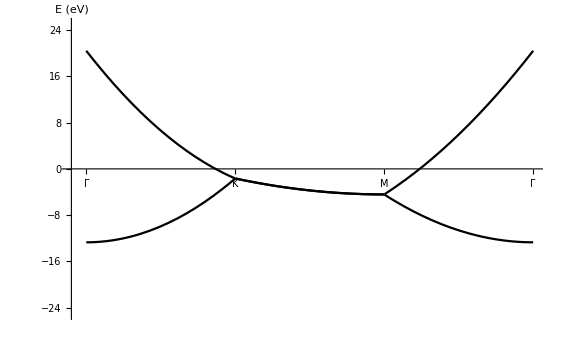

```mathematica
plot1=Plot[e0{E2+Kin[kGammaMKGamma[q]],
E2+Kin[kGammaMKGamma[q]-reciprocalVec[[1]]-reciprocalVec[[2]] ]
},{q,0,3},PlotRange->{-25,25},AxesLabel->Evaluate[Style[#,15]&/@{"","E (eV)"}],PlotStyle->Black,AxesOrigin->{-0.1,0},Ticks->{{{0,"Γ",0.5,Directive[Dashed,Thick,Blue]},{1,"K",0.5,Directive[Dashed,Thick,Blue]},{2,"M",0.5,Directive[Dashed,Thick,Blue]},{3,"Γ",0.5,Directive[Dashed,Thick,Blue]}},Automatic}]
```

```mathematica
E0=e0*(E2+Kin[kGammaMKGamma[1]])
```

-1.65479

```mathematica
t = -e0*(Kin[kGammaMKGamma[0]]-Kin[kGammaMKGamma[0]-reciprocalVec[[1]]])/6
```

5.51634

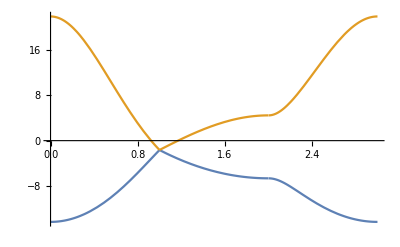

```mathematica
Plot[Evaluate[Sort[ConstantArray[E0,2]+t*Evaluate[Eigenvalues[{Evaluate@h2[kGammaMKGamma[q],t0],Evaluate@S[kGammaMKGamma[q],s0]} ]]/.{s0->0.1,t0->0}]],{q,0,3}]
```

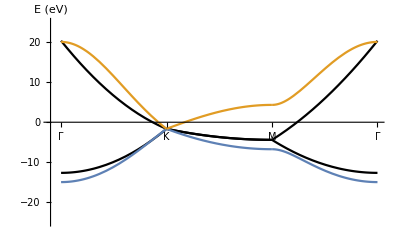

```mathematica
Show[plot1,Plot[Evaluate[Sort[ConstantArray[E0,2]+t*Evaluate[Eigenvalues[{Evaluate@h2[kGammaMKGamma[q],t0],Evaluate@S[kGammaMKGamma[q],s0]} ]]/.{s0->0.08,t0->0}]],{q,0,3}]]
```

```mathematica
eig=Eigenvalues[{h2[kGammaM[0],0],S[kGammaM[0],s0]}]
f1=Simplify[eig[[1]]-eig[[2]]]/.(s0->0)
t1 = -e0*(Kin[kGammaMKGamma[0]]-Kin[kGammaMKGamma[0]-reciprocalVec[[1]]])/6
```

{-3/(-1+3 s0),-3/(1+3 s0)}

6

5.51634

```mathematica
Manipulate[Show[plot1,Plot[{E0,E0}+t1 Eigenvalues[{Evaluate@h2[kGammaMKGamma[q],0],Evaluate@S[kGammaMKGamma[q],s]} ],{q,0,3}]],{s,0.06,0.3,0.01}]
```

```mathematica
eig=Eigenvalues[{h2[kGammaM[0],0],S[kGammaM[0],s0]}]
f1=Simplify[eig[[1]]-eig[[2]]]/.(s0->0.1)
t2 = -e0*(Kin[kGammaMKGamma[0]]-Kin[kGammaMKGamma[0]-reciprocalVec[[1]]])/f1
```

{-3/(-1+3 s0),-3/(1+3 s0)}

6.59341

5.01987

```mathematica
Manipulate[Show[plot1,Plot[{E0,E0}+t2 Eigenvalues[{Evaluate@h2[kGammaMKGamma[q],0],Evaluate@S[kGammaMKGamma[q],s]} ],{q,0,3}]],{s,0.09,0.12,0.001}]
```

## d) Velocidade de grupo

```mathematica
D[ConstantArray[E0,2]+t*Evaluate[Eigenvalues[{Evaluate@h2[kGammaK[q],t0],Evaluate@S[kGammaK[q],s0]} ]]/.{s0->0.08,t0->0},q]/.(q->1)
```

{-20.0111-6.14309×10^-15 ⅈ,20.0111+4.91171×10^-15 ⅈ}

```mathematica
expression=D[t*First@Sort@Eigenvalues[{Evaluate@h2[{kx,ky},t0],Evaluate@S[{kx,ky},s0]} ]/.{s0->0.08,t0->0},{{kx,ky}}];
```

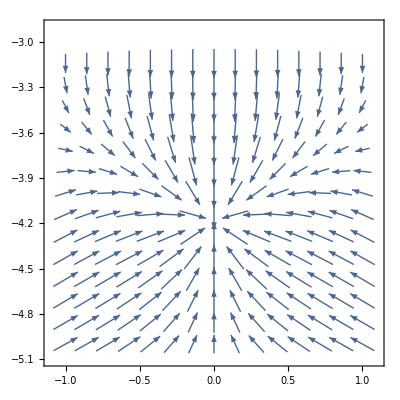

```mathematica
VectorPlot[expression,{kx,-1,+1},{ky,-5,-3}]
```

```mathematica
expression1=t*First@Sort@Eigenvalues[{Evaluate@h2[{kx,ky},t0],Evaluate@S[{kx,ky},s0]} ]/.{s0->0.08,t0->0};
expression3=t*Last@Sort@Eigenvalues[{Evaluate@h2[{kx,ky},t0],Evaluate@S[{kx,ky},s0]} ]/.{s0->0.08,t0->0};
```

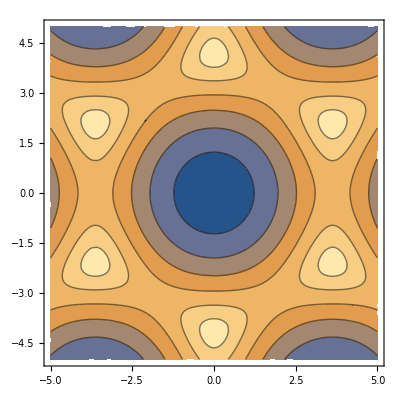

```mathematica
ContourPlot[expression1,{kx,-5,5},{ky,-5,5}]
```

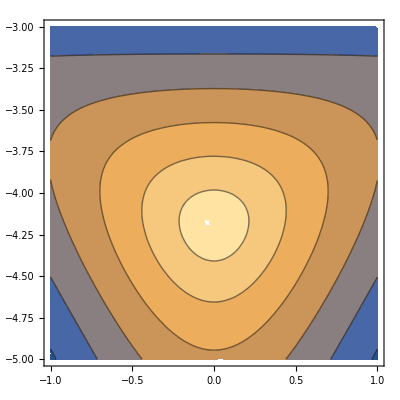

```mathematica
ContourPlot[expression1,{kx,-1,+1},{ky,-5,-3}]
```

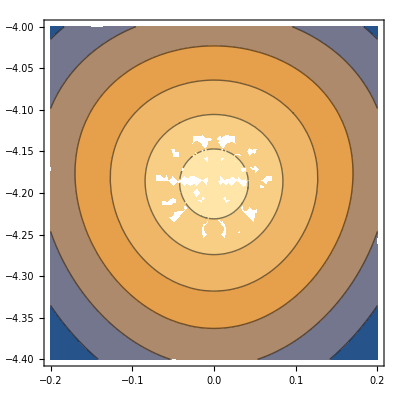

```mathematica
ContourPlot[expression1,{kx,-0.2,0.2},{ky,-4.4,-4}]
```

```mathematica
Norm[2.46*expression/.{kx->0.00001,ky->4Pi/3}]
```

11.7521

```mathematica
Norm[2.46*expression/.{kx->0.00001,ky->4Pi/3}]/(6.58*^-16)
```

1.78604×10^16

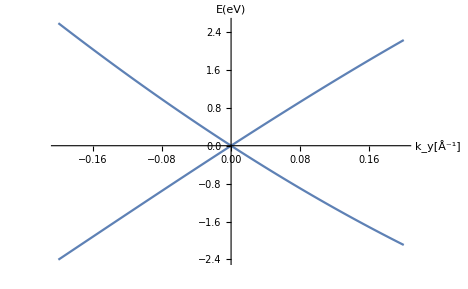

```mathematica
Plot[{expression1,expression3}/.{kx->0,ky->4Pi/3+q*2.46},{q,-0.2,0.2},AxesLabel->{"k_y[Å^-1]","E(eV)"}]
```

## e) Plot 3D

```mathematica
expression2= e0*(E2 +Kin[{kx,ky}]);
```

```mathematica
Plot3D[{ e0*(E2 +Kin[{kx,ky}-reciprocalVec[[1]]]), e0*(E2 +Kin[{kx,ky}+reciprocalVec[[1]]]), e0*(E2 +Kin[{kx,ky}-reciprocalVec[[2]]]), e0*(E2 +Kin[{kx,ky}+reciprocalVec[[2]]]),e0*(E2 +Kin[{kx,ky}-reciprocalVec[[2]]-reciprocalVec[[1]]]),e0*(E2 +Kin[{kx,ky}+reciprocalVec[[2]]+reciprocalVec[[1]]]),expression2},{kx,-8,8},{ky,-8,8},RegionFunction->Function[{kx,ky},f[kx,ky]<0.5],AxesLabel->((Style[#,15])&/@{"k_x","k_y","E(k_x,k_y) [eV]"})]
```

-Graphics3D-

```mathematica
Plot3D[{ Min[e0*(E2 +Kin[{kx,ky}-reciprocalVec[[1]]]), e0*(E2 +Kin[{kx,ky}+reciprocalVec[[1]]]), e0*(E2 +Kin[{kx,ky}-reciprocalVec[[2]]]), e0*(E2 +Kin[{kx,ky}+reciprocalVec[[2]]]),e0*(E2 +Kin[{kx,ky}-reciprocalVec[[2]]-reciprocalVec[[1]]]),e0*(E2 +Kin[{kx,ky}+reciprocalVec[[2]]+reciprocalVec[[1]]])],expression2},{kx,-8,8},{ky,-8,8},RegionFunction->Function[{kx,ky},f[kx,ky]<0.5],AxesLabel->((Style[#,15])&/@{"k_x","k_y","E(k_x,k_y) [eV]"})]
```

-Graphics3D-